# TP frottements 2

## Mesures

La distance est notée “d”.
Les dimensions des billes sont notées au dessus.

```mathematica
di = Quantity[Around[8.5,0.1],"Centimeters"];
d = UnitConvert[di, "Meters"]

bille1diam = Quantity[1,"Millimeters"];
bille2diam = Quantity[1.5,"Millimeters"];
bille3diam = Quantity[2,"Millimeters"];

b1r = N[UnitConvert[bille1diam/2, "Meters"]]
b2r = N[UnitConvert[bille2diam/2, "Meters"]]
b3r = N[UnitConvert[bille3diam/2, "Meters"]]

t1l = Quantity[Around[{4.07,4.15,4.11,4.05,4.18},0.005], "Seconds"]
t2l = Quantity[Around[{1.63,1.83,1.74,1.88,1.77},0.005], "Seconds"]
t3l = Quantity[Around[{1.15,1.14,1.17,1.18,1.14},0.005], "Seconds"]
```

(0.08500.0010) m

0.0005 m

0.00075 m

0.001 m

{(4.0700.005) s,(4.1500.005) s,(4.1100.005) s,(4.0500.005) s,(4.1800.005) s}

{(1.6300.005) s,(1.8300.005) s,(1.7400.005) s,(1.8800.005) s,(1.7700.005) s}

{(1.1500.005) s,(1.1400.005) s,(1.1700.005) s,(1.1800.005) s,(1.1400.005) s}

## Calculs 1

La moyenne des temps a été prise afin de calculer la vitesse.

```mathematica
t1 = Mean[t1l]
t2 = Mean[t2l]
t3 = Mean[t3l]
```

(4.11200.0022) s

(1.77000.0022) s

(1.15600.0022) s

```mathematica
v1 = d/t1
v2 = d/t2
v3 = d/t3
```

(0.020670.00024) m/s

(0.04800.0006) m/s

(0.07350.0009) m/s

## Calculs 2

Le travail de formules pour les forces :

```mathematica
volsp =4/3 π*R^3;
m = ρacier *volsp;

fp= m*g;
fa= ρglyc*volsp*g;
ff=6*π*R*η*vlim;

Factor[Solve[Expand[ff+fa==fp],η]]
```

{{η→(2 g R^2 (ρacier-ρglyc))/(9 vlim)}}

## Calculs 3

Application numérique pour calculer η :

```mathematica
gc = Quantity[9.81,"Meters"/"Seconds"^2];
ρacierc = Quantity[7850,"Kilograms"/"Meters"^3];
ρglycc = Quantity[1260,"Kilograms"/"Meters"^3];

R1 = b1r;
vlim1 = v1;
η1i = (2 gc R1^2 (ρacierc-ρglycc))/(9 vlim1);
η1 =UnitConvert[η1i, "Millipascals"*"Seconds"]

R2 = b2r;
vlim2 = v2;
η2i = (2 gc R2^2 (ρacierc-ρglycc))/(9 vlim2);
η2 =UnitConvert[η2i, "Millipascals"*"Seconds"]

R3 = b3r;
vlim3 = v3;
η3i = (2 gc R3^2 (ρacierc-ρglycc))/(9 vlim3);
η3 = UnitConvert[η3i, "Millipascals"*"Seconds"]
```

(173.72.0) s mPa

(168.32.0) s mPa

(195.42.3) s mPa

Vu que η est une constante pour un liquide à une température donnée, on prend la moyenne pour la suite :

```mathematica
ηf = Mean[{η1,η2,η3}]
 inηre = UnitConvert[ηf[[1]]["Uncertainty"]/ηf[[1]]["Value"],"Percent"]
```

(179.11.2) s mPa

0.685675 %

## Modèle 1

Calcul de formule pour le modèle.

```mathematica
volspm =4/3 π*rm^3;
mm = ρacierm *volspm;

fpm= mm*gm;
fam= ρglycm*volspm*gm;
ffm=6*π*rm*ηm*vm;

Solve[Expand[atot mm==fpm-fam-ffm],atot]
```

{{atot→(-9 vm ηm+2 gm rm^2 ρacierm-2 gm rm^2 ρglycm)/(2 rm^2 ρacierm)}}

## Modèle 2

{{vlimtest→0.180446}}

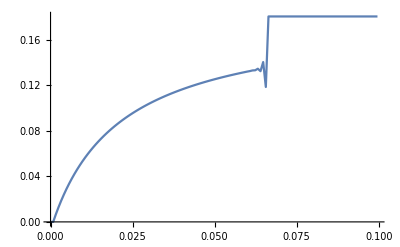

```mathematica
gmp = 9.81;
ρaciermp = 7850;
ρglycmp = 1260;
ηmp = UnitConvert[ηf,"Pascals"*"Seconds"][[1]]["Value"];

rmp = 0.0015;
vop = 0;

const1 = 2 gmp rmp^2 ρaciermp-2 gmp rmp^2 ρglycmp;
const2 = 2 rmp^2 ρaciermp;

Afun[v_] := ((-9 v ηmp + const1)/const2);
Calcfun[v_,t_] := vop+t*Afun[v];

Solve[Afun[vlimtest] == 0,vlimtest]

vlimfun = 0.18044580728859538;
vlist = {vop};
tlist = {0};
Δtfun = 0.00081;
tfun = 0;
vfun = vop;
isfinish = False;
Do[{vfun = Calcfun[vfun, tfun],tfun = tfun+Δtfun, If[vfun ≤ vlimfun && isfinish == False, AppendTo[vlist,vfun], {isfinish = True,AppendTo[vlist,vlimfun]}], AppendTo[tlist,tfun]},0.1/Δtfun]

ListLinePlot[Transpose[{tlist,vlist}]]
```

## Modèle 3

Ne marche pas encore !!!

```mathematica
Afunm[v_] := ((-9 v ηmp + const1)/const2);
Calcfunm[v_,t_,i_] := i+t*Afunm[v];

Manipulate[{tlistm={0},vlistm={vom},isfinishm = False,vfunm=vom,tfunm=0,
Do[{vfun = Calcfun[vfunm, tfunm, vom],tfunm = tfunm+0.1/tmax, If[vfunm ≤ vlimfun && isfinishm == False, AppendTo[vlistm,vfunm], {isfinishm = True,AppendTo[vlistm,vlimfun]}], AppendTo[tlistm,tfunm]},tmax],
ListLinePlot[Transpose[{tlistm,vlistm}]]},
{vom, 0, 1, 0.1},{tmax,0,10000, 100}]
```